```mathematica
APPM 2350 Project 2: Hiking
```

## Defining the Mountain Range

```mathematica
(*creating mountain range*)
m1[x_,y_]=ⅇ^-(1*√((x-1)^2+(y-1.1)^2))^2;
m2[x_,y_]=ⅇ^-(3*√((x-3)^2+(y-2)^2))^2;
m3[x_,y_]=ⅇ^-(1*√((x-4)^2+(y-1)^2))^2;
m4[x_,y_]=ⅇ^-(2*√((x-4)^2+(y-3.5)^2))^2;
m5[x_,y_]=ⅇ^-(3*√((x-3)^2+(y-3.5)^2))^2;
m6[x_,y_]=ⅇ^-(2*√((x-2)^2+(y-3)^2))^2;
m7[x_,y_]=ⅇ^-(2*√((x-4)^2+(y-2)^2))^2;
M[x_,y_]=(1.5*m1[x,y]+0.5*m2[x,y]+0.5*m3[x,y]+1*m4[x,y]+0.75*m5[x,y]+1*m6[x,y]+0.5*m7[x,y])+7;
Mx[x_,y_] = D[M[x,y],x];
Mxx[x_,y_] = D[Mx[x,y],x];
My[x_,y_] = D[M[x,y],y];
Myy[x_,y_] = D[M[x,y],y];
Mxy[x_,y_] = D[Mx[x,y],y];
Gradm[x_,y_]=Grad[My[x,y], {x,y}];
```

## Analyzing the Mountain Range

```mathematica
x[t_]= 2.5 + 1.8*Cos[(4*t)];(*X component of trail path*)
y[t_]= 2 + 1.2*Sin[(4*t)];(*y component of trail path*)
x1[t_] = D[x[t], t];(*first derv of x*)
y1[t_] = D[y[t],t];(*first derv of y*)
r[t_]= {x[t],y[t]};(*vector equation for trail path*)
v[t_] =D[r[t], t];(*derv of vector path r(t) with respect to t*)
u[t_] = Normalize[v[t]];(*unit vector of velocity vector*)
G[t_] = Gradm[x[t], y[t]]; (*Gradient of the mountain range in terms of time*)
d[t_]= Dot[G[t],u[t] ];(*the directional derv is the gradient dotted with the directional unit tangent*)
R[t_]={x[t],y[t],M[x[t],y[t]]};(*3D plot of route*)
```

## Steepest Decent

```mathematica
FindMaximum[Abs[d[t]], {t, 0.28 }](*steepest part of the trail. Indicates that we should be going up that part of the trail *)
R[0.36272532684913966] (*gives us the point on the map*)
```

{5.24767,{t→0.362725}}

{2.71529,3.19139,7.26774}

## Slope Max and Min

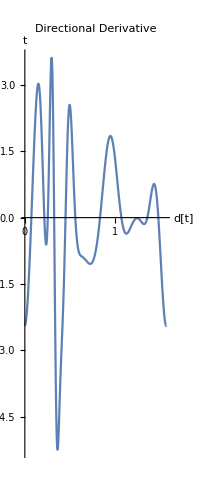

```mathematica
ParametricPlot[{t, d[t]}, {t,0,π/2},PlotLabel->"Directional Derivative",AxesLabel->{"d[t]","t"}, AspectRatio->Full ]
FindMaximum[d[t], {t, 0.28 }](*greatest rate of change/slope*)
FindMinimum[d[t], {t, 0.38}](*least rate of change/slope*)
```

## Highest Points

```mathematica
R[x_,y_]=((x-2.5)/1.8)^2+((y-2)/(-1.2))^2-1; 
Rx[x_,y_]= D[R[x,y], {x}];
Ry[x_,y_]= D[R[x,y], {y}];
FindRoot[{Mx[x,y] == λ*Rx[x,y],My[x,y] == λ*Ry[x,y],R[x,y]== 0},{x,0.9}, {y,1}, {λ, 0}]
(*height at max*)
```

{x→1.11092,y→1.23683,λ→0.375482}

```mathematica
{x->1.1109245153622094,y->1.2368284602388133,λ->0.375481758231771}
M[1.1109245153622094,1.236828460238813](*MAX Height in 1000ft*)
```

{x→1.11092,y→1.23683,λ→0.375482}

8.45429

## Honey Badger

```mathematica
(*honeybadger location*)
badger = {x[π/4],y[π/4]}(*2D*)
badger2={x[π/4],y[π/4],M[x[π/4],y[π/4]]}
(*honey badger slope*)
slope = d[π/4]
```

{0.7,2.}

{0.7,2.,7.60988}

-0.757415

## Lake Mochi

```mathematica
(*gives us the point in the mountain range near 3.1,2.9 where the grad is zero. i.e the lowest point*)
FindRoot[{My[x,y] == 0,Mx[x,y]== 0}, {x,3.1},{y,2.9}]
```

{x→3.11423,y→2.74827}

## Plots

-Graphics3D-

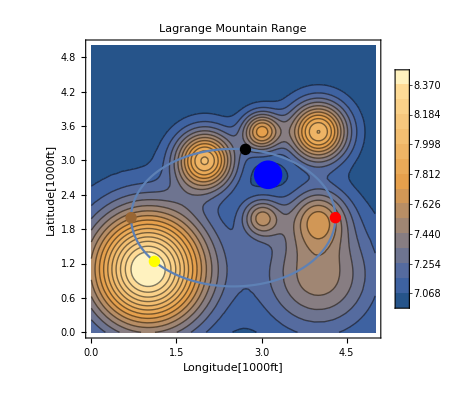

```mathematica
route = ParametricPlot[{x[t],y[t]},{t, 0, π/2}];
route3d = ParametricPlot3D[{x[t],y[t], M[x[t],y[t]]},{t, 0, π/2}];
mountains = Plot3D[M[x,y],{x,0,5},{y,0,5},PlotLabel->"Lagrange Mountain Range",AxesLabel->{"Longitude[1000ft]","Latitude[1000ft]","Altitude[1000ft]"},Mesh->None];
test  = ContourPlot[M[x,y], {x,0,5},{y,0,5},PlotLabel->"Lagrange Mountain Range",AxesLabel->{"Longitude[1000ft]","Latitude[1000ft]"}, Contours->15,PlotLegends->Automatic];
Show[mountains, route3d,Point11,Point13,Point15,Point17,Point5,PlotRange-> All]
Show[test, route,Point12,Point14,Point16,Point18,Point6, PlotRange -> All]
```

```mathematica
{{"Largrange Mountain Range Key", ""}, {"Trail Head", RGBColor[1, 0, 0]}, {"Steepest Desecnt", GrayLevel[0]}, {"Honey Badger", RGBColor[0.6, 0.4, 0.2]}, {"Highest Elevation", RGBColor[1, 1, 0]}, {"Lake Mochi", RGBColor[0, 0, 1]}}
```

```mathematica
Point11=Graphics3D[{Red,Sphere[{4.3,2,7.51705},.14]}];
Point12=Graphics[{Red,Disk[{4.3,2},.1]}];
Point13=Graphics3D[{Black,Sphere[{2.715294365766725,3.191385437411066,7.267735963292981},.14]}];
Point14=Graphics[{Black,Disk[{2.715294365766725,3.191385437411066},.1]}];
Point5=Graphics3D[{Brown,Sphere[{.7,2,7.60988},.14]}];
Point6=Graphics[{Brown,Disk[{.7,2},.1]}];
Point15=Graphics3D[{Yellow,Sphere[{1.11092,1.23683,8.45293},.14]}];
Point16=Graphics[{Yellow,Disk[{1.11092,1.23683},.1]}];
Point17=Graphics3D[{Blue,Sphere[{3.11423,2.74827,7},.25]}];
Point18=Graphics[{Blue,Disk[{3.11423,2.74827},.25]}];
```

```mathematica
ColorD={Red,Black,Brown,Yellow,Blue};
Balls={"Trail Head","Steepest Desecnt","Honey Badger","Highest Elevation","Lake Mochi"};
Key1=Thread[{Balls,ColorD}];
Key2=Grid[Key1,Frame->ALL]
```

```mathematica
ReplacePart[Key2,1->Prepend[First[Key2],{"Largrange Moutain Range Key",""}]]
```